Quantum Computation: Overview |

See also Chapter 2 of the Quantum Workbook (2022)https://doi.org/10.1007/978-3-030-91214-7.

In the simplest physical terms, quantum computation is an implementation of an arbitrary unitary operation on a finite collection of two-level quantum systems that are called quantum bits or qubits for short. It is typically depicted in a quantum circuit diagram as in Figure 1.

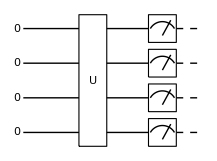
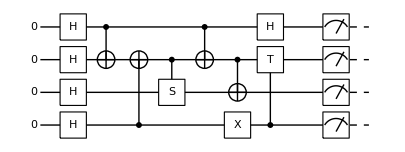
-Graphics-=-Graphics-

Figure 1. The quantum circuit model of quantum computation. (left) The input state from the left is processed by a unitary operator U, and then the output state is measured in the computational basis on the right. (right) A quantum computer is programmable, and the unitary gate U in the left panel is decomposed into elementary gates that act on one qubit or two at each time.

Each qubit is associated with a line that indicates the time evolution of the state specified on the left, and time flows from left to right. The quantum logic gate operations (or gates for short) on single or multiple qubits are denoted by a rectangular box often with labels indicating the types of the gates. Measurements are denoted by square boxes with needles. After a measurement, time-evolution is represented by dashed lines to remind that the information is classical, that is, there is no superposition.

The input state is prepared in one of the states in the logical basis, typically 0⊗0⊗⋯⊗0. After an overall unitary operation, the resulting state is measured in the logical basis, and the readouts are supposed to be the result of the computation.
In order for a quantum computer to be programmable, a given unitary operator Uˆ must be implemented as a combination of other more elementary unitary operators

U=U_1 U_2⋯ U_L

where each U_k is chosen from a small fixed set of elementary gate operations. The latter operations are the elementary quantum logic gates of the quantum computer.

In this collection of tutorial documents, we will examine widely-used choices for elementary gates and illustrate how a set of elementary gates achieve an arbitrary unitary operation to realize the so-called universal quantum computation.

Single-Qubit Gatespaclet:Q3/tutorial/SingleQubitGates

The Pauli Gatespaclet:Q3/tutorial/SingleQubitGates#1574772109

The Hadamard Gatepaclet:Q3/tutorial/SingleQubitGates#347838345

Rotationspaclet:Q3/tutorial/SingleQubitGates#1113797362

Euler Rotationspaclet:Q3/tutorial/SingleQubitGates#1230573581

A Discrete Set of Universal Rotationspaclet:Q3/tutorial/SingleQubitGates#179863498

Two-Qubit Gatespaclet:Q3/tutorial/TwoQubitGates

Controlled-NOT Gate (CNOT)paclet:Q3/tutorial/TwoQubitGates#1585062394

Controlled-Z Gate (CZ)paclet:Q3/tutorial/TwoQubitGates#29167796

Swap Gatepaclet:Q3/tutorial/TwoQubitGates#1218939314

Controlled-Unitary Gatespaclet:Q3/tutorial/TwoQubitGates#1455445268

General Unitary Gatespaclet:Q3/tutorial/TwoQubitGates#1476129218

Multi-Control NOT Gatepaclet:Q3/tutorial/MultiControlNOTGate

The Toffoli Gatepaclet:Q3/tutorial/MultiControlNOTGate#770299810

The Fredkin Gatepaclet:Q3/tutorial/MultiControlNOTGate#1991838106

Implementationspaclet:Q3/tutorial/MultiControlNOTGate#1310796799

Multi-Control Unitary Gatespaclet:Q3/tutorial/MultiControlUnitaryGates

Gray-Code Methodpaclet:Q3/tutorial/MultiControlUnitaryGates#35322904

Quadratic Implementationspaclet:Q3/tutorial/MultiControlUnitaryGates#1081937375

Universal Quantum Computationpaclet:Q3/tutorial/UniversalQuantumComputation

Decomposition into Two-Level Unitary Matricespaclet:Q3/tutorial/UniversalQuantumComputation#1255432361

Implementation of Two-Level Unitary Matrices: Ideapaclet:Q3/tutorial/UniversalQuantumComputation#1012467270

Implementation of Two-Level Unitary Matrices: Gray Code Sequencepaclet:Q3/tutorial/UniversalQuantumComputation#1829642645

Universal Quantum Computation Theorempaclet:Q3/tutorial/UniversalQuantumComputation#1255432361

Computational Model of Measurementpaclet:Q3/tutorial/ComputationalModelOfMeasurement

Measurement in an Arbitrary Basispaclet:Q3/tutorial/ComputationalModelOfMeasurement#58300685

Pauli Measurementspaclet:Q3/tutorial/ComputationalModelOfMeasurement#541468603

| Related Guides
▪Quantum Information Systems

| Related Tech Notes
▪Quantum Information Systems with Q3
▪Quick Quantum Computing with Q3

| Related Links
▪M. Nielsen and I. L. Chuang (2022)https://doi.org/10.1017/CBO9780511976667, Quantum Computation and Quantum Information (Cambridge University Press).
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer).